## Faraday Stability Analysis

### Setting Constants

```mathematica
g=9.81;  (* Gravitational Acceleration (in m/s^2) *)
σ =20.6*10^-3;  (* Surface Tension (in kg/s^2) *)
ρ = 949;  (* Density (in kg/m^3) *)
ω0 = 80 * 2π; (* rad / s *)
ν=0.8025*20*10^-6;(* Viscosity (in m^2/s) *)
ξ=2ν km^2;
```

#### Flat-No Flow situation

```mathematica
Clear[ω,ωg,temp]
```

```mathematica
ω=Sqrt[g km(1+σ/(ρ g) km^2)];
ωg=Sqrt[g km];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

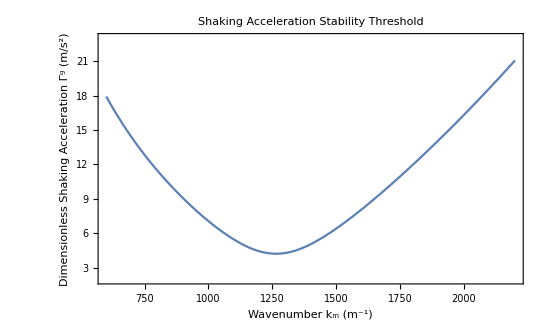

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4.21535,{km→1264.86}}

```mathematica
temp=Solve[(ω^2+ξ^2−1/4 ω0^2)^2+ω0^2 ξ^2−1/4(ωg^2 Γg)^2==0,Γg][[2]];
Plot[Γg/.temp,{km,600,2200},PlotRange->{2,23},
	Frame->True,
	Axes->False,
	FrameLabel->{"Wavenumber  k_m  (m^-1)","Dimensionless Shaking Acceleration Γ^g (m/s^2)"},
	PlotLabel->"Shaking Acceleration Stability Threshold"]
FindMinimum[Γg/.temp,{km,1000}]
```

#### Curved-With Flow situation

```mathematica
Clear[ω,ωg,Γg]
```

```mathematica
d0=1*10^-3; (* m *)
d=0.1Abs[x]+d0; (* depth (m) *)
d/.x->0.19
ω=v km +Sqrt[g km(1+σ/(ρ g) km^2)Tanh[km d]];
ωg=Sqrt[g km];
```

0.02

```mathematica
Γg[km_,x_,v_] =2/ωg^2 Sqrt[((ω^2+ξ^2−1/4 ω0^2)^2+ω0^2 ξ^2)] ;
Manipulate[Plot[Γg[km,x,v],{km,600,2200},PlotRange->{2,23},
	Frame->True,
	Axes->False,
	FrameLabel->{"Wavenumber  k_m  (m^-1)","Dimensionless Shaking Acceleration Γ^g (m/s^2)"},
	PlotLabel->"Shaking Acceleration Stability Threshold under influence of Background Flow"],{{v,0.0,"flow speed  v  (m s^-1)"},0,0.10,0.005},{{x,0.2,"horizontal position  x  (m)"},0,0.2,0.001}]
FindMinimum[Γg[km,0.19,0.025],{km,1000}]
N[Tanh[901 (d0+0.1Abs[0])]]
```

{3.84857,{km→1158.31}}

0.716784

```mathematica
3.4/3.84857
```

0.883445